## Assignment 5

2.2.7 (v)

(7)(a) Find particular solutions to the  following boundary-value problems using Fourier methods.

(b) Plot the particular solutions.

(c) Find homogeneous solutions to match the boundary conditions and solve the full problem.  Plot the full solution.

(v) (ⅆ^3 ϕ)/(ⅆ x^3)-2(ⅆ^2 ϕ)/(ⅆ x^2)+ ⅆϕ/ⅆx-2ϕ=x^2 cos x,ϕ(0)=0,ϕ'(0)=2,ϕ(3)=0 .

### Solution

#### (a,b)

Use ϕ_p(x) = ∑_(n=-∞)^∞ ϕ_n ⅇ^(-ⅈ 2 π n x/L), where L = 3. Then we obtain
 ∑_(n=-∞)^∞ ϕ_n ⅇ^(-ⅈ 2 π n x/L)((-ⅈ 2 π n /L)^3 -2(-ⅈ 2 π n /L)^2+(-ⅈ 2 π n /L)-2) = x^2 cos x. Mulitply both sides by ⅇ^(ⅈ 2 π n x/L) and integrate from 0 to L to obtain
ϕ_n ((-ⅈ 2 π n /L)^3 -2(-ⅈ 2 π n /L)^2+(-ⅈ 2 π n /L)-2)  = f_n  where

f_n = 1/L ∫_0^L x^2 cos x ⅇ^(ⅈ 2 π n x/L)ⅆx.

```mathematica
Clear["Global`*"]
```

```mathematica
L=3;
```

```mathematica
f[n_] = 1/L Integrate[x^2 Cos[x] Exp[I 2 Pi n x/L],{x,0,L}]
```

1/((-9+4 n^2 π^2)^3)9 (-4 ⅈ n π (27+4 n^2 π^2)+2 ⅇ^(2 ⅈ n π) (-81+n π (-27 ⅈ+16 n^2 π^2 (5 ⅈ+n π (1-ⅈ n π)))) Cos[3]-3 ⅇ^(2 ⅈ n π) (63+8 n π (-9 ⅈ+2 n π (-6+n π (2 ⅈ+n π)))) Sin[3])

```mathematica
f[0] = Limit[f[n],n->0]
```

2 Cos[3]+(7 Sin[3])/3

```mathematica
fapprox[x_] = Sum[f[n]  Exp[-I 2 Pi n x/L],{n,-10,10}];
```

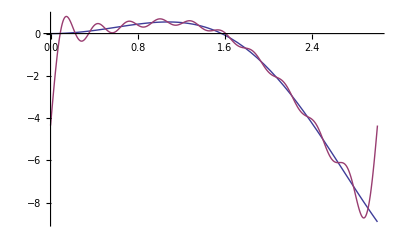

```mathematica
Plot[{x^2 Cos[x], fapprox[x]},{x,0,L}]
```

Our Fourier expansion seems to be working OK, except for Gibb's phenomoenon. Foruntately, the high n components responsible for this will be wiped out in ϕ_p(x):

```mathematica
k[n_] = 2 Pi n/L;
```

```mathematica
ϕ[n_] := f[n]/((-ⅈ k[n])^3 -2 (-ⅈ k[n])^2 - ⅈ k[n] - 2)
```

```mathematica
ϕp[x_] = Sum[ϕ[n]  Exp[-I 2 Pi n x/L],{n,-10,10}];
```

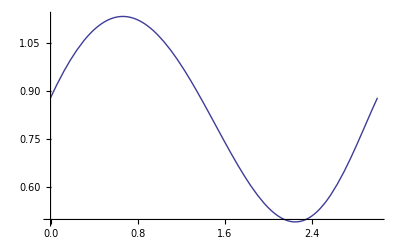

```mathematica
Plot[ϕp[x],{x,0,L}]
```

How do we know this is right? Substitute it into the ODE:

```mathematica
ϕp'''[x] - 2 ϕp''[x] + ϕp'[x] -2 ϕp[x] -x^2 Cos[x] ;
```

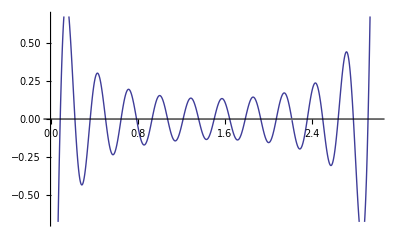

```mathematica
Plot[%,{x,0,L}]
```

Oscillation around zero due to Gibb's phenomenon, (we tookup to 3 derivatives of our solution, which blows up small errors!)

#### (c)

Homogeneous solution: the characteristic polynomial is

```mathematica
s^3 -2s^2 + s -2
```

-2+s-2 s^2+s^3

```mathematica
Solve[%==0,s]
```

{{s→-ⅈ},{s→ⅈ},{s→2}}

So the general homogeneous solution is

```mathematica
ϕh[x_] = C1 Exp[-ⅈ x] + C2 Exp[ⅈ x] + C3 Exp[2 x];
```

Add in the particular solution from part (b)

```mathematica
ϕ[x_] = ϕh[x] + ϕp[x];
```

```mathematica
NSolve[{ϕ[0]==0,ϕ'[0]==2,ϕ[3]==0},{C1,C2,C3}]
```

{{C1→-0.437611+0.636525 ⅈ,C2→-0.437611-0.636525 ⅈ,C3→-0.00477436+1.08463×10^-20 ⅈ}}

```mathematica
ϕ[x_] = ϕ[x]/.%[[1]];
```

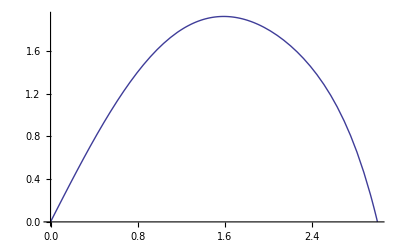

```mathematica
Plot[ϕ[x],{x,0,L}]
```

2.3.1(d)

(1) Find the Fourier transform for the following functions. Use time transform conventions for functions of t, and space transform conventions for functions of x. Except where indicated, do the required integrals by hand. (You may check your results using Mathematica.)

(d) f(x) =x/(1 + x^2).   (You may use Mathematica  to help with the required integral.)

### Solution

I will use the spatial version of the foruier transform. No marks off for using the time version.

```mathematica
ft[k_] = Integrate[x/(1+x^2) Exp[-I k x],{x,-Infinity,Infinity},Assumptions->k∈Reals]
```

-ⅈ ⅇ^(-Abs[k]) π Sign[k]

2.3.2(d)

(2) Verify by hand that the inverse transform of the functions f̃(ω) found in Exercise (1) returns to the listed functions. [You may use Mathematica to help check integrals, and you may also use results such as Eq. (2.3.47) or  Eq. (2.3.76) without proving them.]

### Solution

The inverse transform is ∫_(-∞)^∞ ⅆk/(2π)exp(ⅈ k x) f̃(k). Since f̃(k) is an odd function of k in this case, only the odd part of exp(i k x) survives, and so  the integral can be written as 2∫_0^∞ ⅆk/(2π)ⅈ sin( k x) f̃(k)=∫_0^∞ ⅆk/(π)sin( k x) π exp(-k) . This integral can be done by hand by writing it as (Im∫)_0^∞ⅆk exp(-k+ ⅈ k x)=Im (1/(1-ⅈ x))=x/(1+x^2). QED.

2.3.8

(8) Find the value of the integral ∫_(-∞)^∞ ⅇ^(-ν |t_o|)cos ω_o (t-t_o)ⅆ t_o using the convolution theorem. Use paper and pencil methods to do all required transforms and inverse transforms.

### Solution

Noting that h(t)=∫_(-∞)^∞ f(t_o)g(t-t_o)ⅆ t_owhere f(t_0)=ⅇ^(-ν |t_o|)and g(t)=cos ω_o t we use the convolution theorem, h̃(ω)=f̃(ω)g̃(ω). First, g̃(ω)=π [ δ(ω-ω_o)+δ(ω+ω_o)]. Second, 
f̃(ω) = 2 Re ∫_0^∞ ⅇ^(-ν t + ⅈ ω t)ⅆt =Re 2/(ν-ⅈ ω)=(2 ν)/(ν^2+ω^2).

Therefore, h(t) = ∫_(-∞)^∞ (2 ν)/(ν^2+ω^2)π [ δ(ω-ω_o)+δ(ω+ω_o)]ⅇ^(-ⅈ ω t)ⅆω/(2 π)
=(2 ν)/(ν^2+ω_o^2)cos ω_o t.

Check:

```mathematica
Integrate[Exp[-ν Abs[t0]] Cos[ω0(t-t0)],{t0,-Infinity,Infinity}]
```

If[Im[ω0]==0&&Re[ν]>0,(2 ν Cos[t ω0])/(ν^2+ω0^2),∫_(-∞)^∞ ⅇ^(-ν Abs[t0]) Cos[(t-t0) ω0]ⅆt0]

2.3.10(b)

(10) Evaluate the following integrals by hand:

(b) ∫_(-∞)^∞ δ(cos  t)/t^2ⅆt.

### Solution

cos t=0 at t_n=(n+1/2)π, n∈Integers. Furthermore |sint_n|=1 So ,  ∫_(-∞)^∞ δ(cos  t)/t^2ⅆt=∑_(n=-∞)^∞ 1/t_n^2

```mathematica
Sum[1/(Pi (n+1/2))^2,{n,-Infinity,Infinity}]
```

1

Therefore, ∫_(-∞)^∞ δ(cos  t)/t^2ⅆt=1.